# NONs of N=3,d=1, (2_1_1 configurated) Harmonium; With spin; isotropic trap

## 1) Definitions

### Basic Definitions

```mathematica
(*Define particle Number, here Np, and number of dimensions d*)
```

```mathematica
Np =5;
d = 1;
```

```mathematica
(*Definition of the tuples; in Harmonium document these are the Subscript[t, i][γ] where γ is the index of the inner list and i is the index of the outer list; first list is the list of contributions of the spin up part, second list is the list of contributions of the spin down part*)
```

```mathematica
ttSpinUp={0,1};
ttSpinDown = {0,1,2};
```

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
```

```mathematica
p[a_,b_,Np_]:=Sqrt[b/(a-b(Np-1))];
q[x_,y_,a_,b_,Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x+y));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=t and l_-=s*)
```

```mathematica
A[t_]:=1/(2 t^2);
B[s_,t_,N_]:=-1/(2N) (1/s^2-1/t^2);
sab[a_,b_,n_]:=Sqrt[-1/(2(b*n-a))];
ta[a_]:=Sqrt[1/2a]
l[s_,t_]:=1/((((Np-1) s^2+t^2)/(s^4 t^2+(Np-1) s^2 t^4))^(1/4))
bn[a_,b_,n_]:=((n-1)*b^2/(a-(n-1*b)));
an[a_,b_,n_]:=a-b-1/2*bn[a,b,n]
lf[a_,b_,n_]:=(4*an[a,b,n]^2-bn[a,b,n])^(-1/4)
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
```

```mathematica
c[s_,t_,N_]:=Sqrt[N/((N-1) t^2+s^2)];
d0[s_,t_,N_]:=Sqrt[((N-1) s^2 +t^2)/(N s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
```

```mathematica
Q[s_,t_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### Advanced Definitions resulting from calculation of sections 2 and 3 below

```mathematica
(*The following definitions are derived in subsequent sections; they are just added here for convenience when restarting the kernel*)
```

```mathematica
FpolySpinUp[x1_,y1_,a_,b_]:=1/(a-2 b)^2 π (2 b^2+4 a^3 x1 y1+a b (-3+b (5 x1+y1) (x1+5 y1))+a^2 (1-2 b (x1^2+10 x1 y1+y1^2)));
FpolySpinDown[x1_,y1_,a_,b_]:=π;
```

```mathematica
efun[x_,y_,a_,b_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x^2+y^2)] Exp[b^2(Np-1)/(a-b(Np-1)) x y];
```

```mathematica
normPre[a_,b_]:=((3 π^(3/2))/(√2 √((a (a-3 b))/(a-2 b))))^(-1);
```

```mathematica
(*Define the all-over norm as a function of l_+=t and l_-=s*)
```

```mathematica
norm[s_,t_]:=normPre[A[t],B[s,t,Np]];
```

```mathematica
(*The following defines the powers and the coefficients of the F-polynomial:*)
```

```mathematica
(*Determine the coefficients of the F polynomial 'Fpoly' by the coefficient function of Mathematica and for 0,0,0,0 by evaluating Fpoly at x1=x2=y1=y2=0. This is the real number coefficient of  (x^(γ=1))^Subscript[n, 1] (x^(γ=2))^Subscript[n, 2] ((x̃)^(γ=1))^Subscript[m, 1] ((x̃)^(γ=2))^Subscript[m, 2]  ;;; again there are two parts for spin up and spin down *)
```

```mathematica
coefSpinUp[n1_,m1_,a_,b_]:=1/n1!  1/m1!   D[FpolySpinUp[x1,y1,a,b],{x1,n1},{y1,m1}]/.{x1->0,y1->0};
coefSpinDown[n1_,m1_,a_,b_]:=1/n1!  1/m1!   D[FpolySpinDown[x1,y1,a,b],{x1,n1},{y1,m1}]/.{x1->0,y1->0};
```

```mathematica
(*Determine the maximum degree of Fpoly in its arguments, again there are two parts for spin up and spin down*)
```

```mathematica
maxDegreeSpinUpx1 = Exponent[FpolySpinUp[x1,y1,a,b],x1];
maxDegreeSpinUpy1= Exponent[FpolySpinUp[x1,y1,a,b],y1];
maxDegreeSpinDownx1 = Exponent[FpolySpinDown[x1,y1,a,b],x1];
maxDegreeSpinDowny1= Exponent[FpolySpinDown[x1,y1,a,b],y1];
```

### 4.1) Definition of creation and annihilation operators, the integral monomials and the indicator functions

```mathematica
(*Define the action of x and y operators on the Hermite functions, note that X is already dimensionless, i.e. X=x/l; in this mathematica file, z[n,m] denotes the product of two Hermite functions of natural length 1 and degrees n and m: z[n,m]=Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)) *)
```

```mathematica
X[z[n_,m_]]:=(Sqrt[n+1]/Sqrt[2]z[n+1,m]+Sqrt[n]/Sqrt[2]z[n-1,m])//Expand
Y[z[n_,m_]]:=(Sqrt[m+1]/Sqrt[2]z[n,m+1]+Sqrt[m]/Sqrt[2]z[n,m-1])//Expand
```

```mathematica
X[0]:=0
X[fac1_ z[n_,m_]]:=fac1 X[z[n,m]]//Expand
X[z1_+z2_]:=X[z1]+X[z2]//Expand
Y[0]:=0
Y[fac1_ z[n_,m_]]:=fac1 Y[z[n,m]]//Expand
Y[z1_+z2_]:=Y[z1]+Y[z2]//Expand
```

```mathematica
(* Mon[r_,s_,n_,m_]:= Y^s[X^r[z[n,m]]], so it represents y^s x^r Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)) for a fixed spatial dimension parameter γ*)
```

```mathematica
Mon[r_,s_,n_,m_]:=Nest[Y,Nest[X,z[n,m],r],s]
```

```mathematica
(*Example:*)
```

```mathematica
Mon[2,4,0,0]
```

3/8 z[0,0]+(3 z[0,2])/(2 √2)+1/2 √(3/2) z[0,4]+(3 z[2,0])/(4 √2)+3/2 z[2,2]+1/2 √3 z[2,4]

```mathematica
(*Define the function ip which is the result of the integration over variables of one spatial dimension; note that we have ∫dx^(γ) dy^(γ) ((∑_(k=0))^∞ q^k  (y^s x^r Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)))_(= M[s,r,n,m]) · Subscript[ϕ, k]^(1)(x^(γ)) +× Subscript[ϕ, k]^(1)(y^(γ)) )*)
```

```mathematica
ip[z[r_,s_],lm_,lp_]:=If[r-s==0,Q[lm,lp]^r,0];
```

```mathematica
ip[0]:=0
ip[fac1_ z[n_,m_],lm_,lp_]:=fac1 ip[z[n,m],lm,lp]//Expand
ip[z1_+z2_,lm_,lp_]:=ip[z1,lm,lp]+ip[z2,lm,lp]//Expand
```

```mathematica
(*Define the labels of the (multidimensional) bosonic eigenfunctions, which are products of the single-particle functions, for a derivation in case of d=3 see mathematica file 'finding the ind3 function':*)
```

```mathematica
ind1[k_]:=Floor[-1/2+Sqrt[2(k-1)+1/4]]-(k-1-Binomial[Floor[-1/2+Sqrt[2(k-1)+1/4]]+1,2]);
```

### Definition of the explicit 1 - RDO matrix element calculator (taken from 4.2)

```mathematica
(*Define the accuracy used in the calculations below*)
```

```mathematica
acc = 16;
```

```mathematica
(*Eventually, the matrix elements are determined; the infinite dimensional matrix is truncated at dim×dim and then displayed by using the MatrixForm command of Mathematica*)
```

```mathematica
rhoSpinUp[dim_,lm_,lp_]:=
N[norm[lm,lp]Sqrt[Pi]^2 l[lm,lp]^2Sqrt[1-Q[lm,lp]^2]^2*
Sum[
If[coefSpinUp[n1,m1,A[lp],B[lm,lp,Np]]==0,Table[0,{g,1,dim},{h,1,dim}],
coefSpinUp[n1,m1,A[lp],B[lm,lp,Np]]  l[lm,lp]^(n1+m1) *
Table[
ip[Mon[n1,m1,ind1[g],ind1[h]],lm,lp],
{g,1,dim},{h,1,dim}]],
{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}
],acc]
```

```mathematica
rhoSpinDown[dim_,lm_,lp_]:=
N[norm[lm,lp]Sqrt[Pi]^2 l[lm,lp]^2Sqrt[1-Q[lm,lp]^2]^2*
Sum[
If[coefSpinDown[n1,m1,A[lp],B[lm,lp,Np]]==0,Table[0,{g,1,dim},{h,1,dim}],
coefSpinDown[n1,m1,A[lp],B[lm,lp,Np]]  l[lm,lp]^(n1+m1) *
Table[
ip[Mon[n1,m1,ind1[g],ind1[h]],lm,lp],
{g,1,dim},{h,1,dim}]],
{n1,0,maxDegreeSpinDownx1},{m1,0,maxDegreeSpinDowny1}
],acc]
```

## 2) Calculation of the F polynomial, bosonic exp function of ρ and normalisation factor N

```mathematica
(*Define the inner polynomial of eq. 2.24 of Harmonium1 document; in the conventions of this document, xi is the x^(γ) coordinate with γ=i, yj is the (x̃)^(γ) coordinate with γ=j, there are now two contributions from the spin up and spin down part:*)
```

```mathematica
polyPre2SpinUp[x1_,y1_,a_,b_,u_]:=Expand[Sum[(2^ttSpinUp[[k]]  (ttSpinUp[[k]]!))^(-1)  * 
HermiteH[ttSpinUp[[k]],p[a,b,Np]u+q[x1,y1,a,b,Np]] HermiteH[ttSpinUp[[k]],p[a,b,Np]u +q[y1,x1,a,b,Np]],
{k,1,Length[ttSpinUp]}]];
polyPre2SpinDown[x1_,y1_,a_,b_,u_]:=Expand[Sum[(2^ttSpinDown[[k]]  (ttSpinDown[[k]]!))^(-1) * 
HermiteH[ttSpinDown[[k]],p[a,b,Np]u+q[x1,y1,a,b,Np]] HermiteH[ttSpinDown[[k]],p[a,b,Np]u +q[y1,x1,a,b,Np]],
{k,1,Length[ttSpinDown]}]];
(*Perform the integration to get F of 2.24, again there are two parts, each for the spin up or spin down polynomials*)
```

```mathematica
Integrate[Exp[-u^2]polyPre2SpinUp[x1,y1,a,b,u],{u,-∞,∞}]
```

(√π (12 b^2+4 a^3 x1 y1+a b (-7+b (9 x1+y1) (x1+9 y1))+a^2 (1-2 b (x1^2+18 x1 y1+y1^2))))/(a-4 b)^2

```mathematica
Integrate[Exp[-u^2]polyPre2SpinDown[x1,y1,a,b,u],{u,-∞,∞}]
```

1/(2 (a-4 b)^4)√π (816 b^4+16 a^6 x1^2 y1^2-4 a^5 (x1^2-2 x1 y1+4 b x1^3 y1+y1^2+72 b x1^2 y1^2+4 b x1 y1^3)-4 a^3 b (12+b^2 (9 x1+y1) (x1+9 y1) (x1^2+18 x1 y1+y1^2)+3 b (37 x1^2-46 x1 y1+37 y1^2))-8 a b^3 (99+b (187 x1^2-74 x1 y1+187 y1^2))+a^2 b^2 (291+b^2 (9 x1+y1)^2 (x1+9 y1)^2+2 b (659 x1^2-538 x1 y1+659 y1^2))+a^4 (3+4 b (17 x1^2-28 x1 y1+17 y1^2)+4 b^2 (x1^4+54 x1^3 y1+490 x1^2 y1^2+54 x1 y1^3+y1^4)))

```mathematica
(*Define the two F polynomials according to 3.9 of Harmonium1 document*)
```

```mathematica
FpolySpinUp[x1_,y1_,a_,b_]:=(√π (12 b^2+4 a^3 x1 y1+a b (-7+b (9 x1+y1) (x1+9 y1))+a^2 (1-2 b (x1^2+18 x1 y1+y1^2))))/(a-4 b)^2;
FpolySpinDown[x1_,y1_,a_,b_]:=1/(2 (a-4 b)^4)√π (816 b^4+16 a^6 x1^2 y1^2-4 a^5 (x1^2-2 x1 y1+4 b x1^3 y1+y1^2+72 b x1^2 y1^2+4 b x1 y1^3)-4 a^3 b (12+b^2 (9 x1+y1) (x1+9 y1) (x1^2+18 x1 y1+y1^2)+3 b (37 x1^2-46 x1 y1+37 y1^2))-8 a b^3 (99+b (187 x1^2-74 x1 y1+187 y1^2))+a^2 b^2 (291+b^2 (9 x1+y1)^2 (x1+9 y1)^2+2 b (659 x1^2-538 x1 y1+659 y1^2))+a^4 (3+4 b (17 x1^2-28 x1 y1+17 y1^2)+4 b^2 (x1^4+54 x1^3 y1+490 x1^2 y1^2+54 x1 y1^3+y1^4)));
```

```mathematica
(*Define the bosonic exponential function of the first line of 3.9 of Harmonium1 document: efun = (exp[(Subscript[B, N] + Subscript[C, N] - A)(x^(γ) + (x̃)^(γ)) + 2 Subscript[C, N] x^(γ) (x̃)^(γ)]); this is not the product of the exponential functions yet!; in the spin-case the normalisation factor can be determined by using Tr(ρ)=1; at first the spin degrees of freedom will be traced out, leaving the sum of the two Fpoly functions. These in turn will then be integrated to yield the normalisation factor*)
```

```mathematica
efun[x_,y_,a_,b_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x^2+y^2)] Exp[b^2(Np-1)/(a-b(Np-1)) x y];
```

```mathematica
(*Determine the normalisation factor N^2 in eq. 2.24 of Harmonium1 document, note that the first conditional expression is always fulfilled for N≥4*)
```

```mathematica
Integrate[efun[x1,x1,a,b]*(FpolySpinUp[x1,x1,a,b]+FpolySpinDown[x1,x1,a,b]),{x1,-∞,+∞}, Assumptions-> a>0 && b>0]
```

ConditionalExpression[(√2 (2 a^3-22 a^2 b+79 a b^2-94 b^3) π)/((a-5 b) √((a (a-5 b))/(a-4 b)) (a-3 b)^2), a<4 b||a>5 b]

```mathematica
(*Note: Same normalisation as in the (2_2 configuration) case*)
```

```mathematica
Integrate[efun[x1,x1,a,b](FpolySpinUp[x1,x1,a,b]+FpolySpinDown[x1,x1,a,b]),{x1,-∞,+∞}, Assumptions-> a>0 && b<0]
```

(5 π)/(√2 √((a (a-5 b))/(a-4 b)))

```mathematica
(*Therefore the prenorm factor in 2.24 of the Harmonium1 document is given by*)
```

```mathematica
normPre[a_,b_]:=((5 π)/(√2 √((a (a-5 b))/(a-4 b))))^(-1);
```

```mathematica
(*Define the all-over norm as a function of l_+=t and l_-=s*)
```

```mathematica
norm[s_,t_]:=normPre[A[t],B[s,t,Np]];
```

```mathematica
efun[x1,x1p,a,b]*normPre[a,b]*FpolySpinDown[x1,x1p,a,b]
```

1/(2 (a-3 b)^2 √((2 a-6 b)/(a^2-4 a b)) √π)ⅇ^((4 b^2 x1 x1p)/(a-4 b)+(-a+b+(2 b^2)/(a-4 b)) (x1^2+x1p^2)) (6 b^2+4 a^3 x1 x1p+a b (-5+b (7 x1+x1p) (x1+7 x1p))+a^2 (1-2 b (x1^2+14 x1 x1p+x1p^2)))

```mathematica
1/3 √((a (a-3 b))/(a-2 b)) ⅇ^((2 b^2 x1 x1p)/(a-2 b)+(-a+b+b^2/(a-2 b)) (x1^2+x1p^2)) √(2/π) // Simplify
```

1/3 √((a (a-3 b))/(a-2 b)) ⅇ^((2 b^2 x1 x1p)/(a-2 b)+(-a+b+b^2/(a-2 b)) (x1^2+x1p^2)) √(2/π)

## 3) Coefficients of the F polynomial

```mathematica
(*Determine the coefficients of the F polynomial 'Fpoly' by the coefficient function of Mathematica and for 0,0,0,0 by evaluating Fpoly at x1=x2=y1=y2=0. This is the real number coefficient of  (x^(γ=1))^Subscript[n, 1] (x^(γ=2))^Subscript[n, 2] ((x̃)^(γ=1))^Subscript[m, 1] ((x̃)^(γ=2))^Subscript[m, 2]  ;;; again there are two parts for spin up and spin down *)
```

```mathematica
coefSpinUp[n1_,m1_,a_,b_]:=1/n1!  1/m1!   D[FpolySpinUp[x1,y1,a,b],{x1,n1},{y1,m1}]/.{x1->0,y1->0};
coefSpinDown[n1_,m1_,a_,b_]:=1/n1!  1/m1!   D[FpolySpinDown[x1,y1,a,b],{x1,n1},{y1,m1}]/.{x1->0,y1->0};
```

```mathematica
(*Determine the maximum degree of Fpoly in its arguments, again there are two parts for spin up and spin down*)
```

```mathematica
maxDegreeSpinUpx1 = Exponent[FpolySpinUp[x1,y1,a,b],x1];
maxDegreeSpinUpy1= Exponent[FpolySpinUp[x1,y1,a,b],y1];
maxDegreeSpinDownx1 = Exponent[FpolySpinDown[x1,y1,a,b],x1];
maxDegreeSpinDowny1= Exponent[FpolySpinDown[x1,y1,a,b],y1];
```

```mathematica
(*Display the coefficients of the spin up part in a table:*)
```

```mathematica
Join[{{Subscript[n, 1],Subscript[m, 1],"coef"}},Flatten[Table[{n1,m1,coefSpinUp[n1,m1,a,b]//Simplify},{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}],3]]//TableForm
```

n_1 | m_1 | coef
0 |  | 
0 |  | 
((a-2 b) √π)/(a-3 b) |  | 
0 |  | 
1 |  | 
0 |  | 
0 |  | 
2 |  | 
-(a (2 a-7 b) b √π)/(a-3 b)^2 |  | 
1 |  | 
0 |  | 
0 |  | 
1 |  | 
1 |  | 
(2 a (2 a^2-14 a b+25 b^2) √π)/(a-3 b)^2 |  | 
1 |  | 
2 |  | 
0 |  | 
2 |  | 
0 |  | 
-(a (2 a-7 b) b √π)/(a-3 b)^2 |  | 
2 |  | 
1 |  | 
0 |  | 
2 |  | 
2 |  | 
0 |  |

```mathematica
(*Display the coefficients of the spin down part in a table:*)
```

```mathematica
Join[{{Subscript[n, 1],Subscript[m, 1],"coef"}},Flatten[Table[{n1,m1,coefSpinDown[n1,m1,a,b]//Simplify},{n1,0,maxDegreeSpinDownx1},{m1,0,maxDegreeSpinDowny1}],3]]//TableForm
```

n_1 | m_1 | coef
0 |  | 
0 |  | 
((a-2 b) √π)/(a-3 b) |  | 
0 |  | 
1 |  | 
0 |  | 
0 |  | 
2 |  | 
-(a (2 a-7 b) b √π)/(a-3 b)^2 |  | 
1 |  | 
0 |  | 
0 |  | 
1 |  | 
1 |  | 
(2 a (2 a^2-14 a b+25 b^2) √π)/(a-3 b)^2 |  | 
1 |  | 
2 |  | 
0 |  | 
2 |  | 
0 |  | 
-(a (2 a-7 b) b √π)/(a-3 b)^2 |  | 
2 |  | 
1 |  | 
0 |  | 
2 |  | 
2 |  | 
0 |  |

```mathematica
(*Example*)
```

```mathematica
coefSpinUp[0,1,a,b]
```

0

```mathematica
(*Check that the decomposition in coefficients is correct*)
```

```mathematica
Sum[coefSpinUp[n1,m1,a,b]*x1^n1*y1^m1,{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}]-FpolySpinUp[x1,y1,a,b]//Simplify
```

0

```mathematica
Sum[coefSpinDown[n1,m1,a,b]*x1^n1*y1^m1,{n1,0,maxDegreeSpinDownx1},{m1,0,maxDegreeSpinDowny1}]-FpolySpinDown[x1,y1,a,b]//Simplify
```

0

## 4) Evaluation of the matrix elements of ρ; Definition of the action of x operators on Hermite functions

### 4.1) Definition of creation and annihilation operators, the integral monomials and the indicator functions

```mathematica
(*Define the action of x and y operators on the Hermite functions, note that X is already dimensionless, i.e. X=x/l; in this mathematica file, z[n,m] denotes the product of two Hermite functions of natural length 1 and degrees n and m: z[n,m]=Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)) *)
```

```mathematica
X[z[n_,m_]]:=(Sqrt[n+1]/Sqrt[2]z[n+1,m]+Sqrt[n]/Sqrt[2]z[n-1,m])//Expand
Y[z[n_,m_]]:=(Sqrt[m+1]/Sqrt[2]z[n,m+1]+Sqrt[m]/Sqrt[2]z[n,m-1])//Expand
```

```mathematica
X[0]:=0
X[fac1_ z[n_,m_]]:=fac1 X[z[n,m]]//Expand
X[z1_+z2_]:=X[z1]+X[z2]//Expand
Y[0]:=0
Y[fac1_ z[n_,m_]]:=fac1 Y[z[n,m]]//Expand
Y[z1_+z2_]:=Y[z1]+Y[z2]//Expand
```

```mathematica
(* Mon[r_,s_,n_,m_]:= Y^s[X^r[z[n,m]]], so it represents y^s x^r Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)) for a fixed spatial dimension parameter γ*)
```

```mathematica
Mon[r_,s_,n_,m_]:=Nest[Y,Nest[X,z[n,m],r],s]
```

```mathematica
(*Example:*)
```

```mathematica
Mon[2,4,0,0]
```

3/8 z[0,0]+(3 z[0,2])/(2 √2)+1/2 √(3/2) z[0,4]+(3 z[2,0])/(4 √2)+3/2 z[2,2]+1/2 √3 z[2,4]

```mathematica
(*Define the function ip which is the result of the integration over variables of one spatial dimension; note that we have ∫dx^(γ) dy^(γ) ((∑_(k=0))^∞ q^k  (y^s x^r Subscript[ϕ, n]^(1)(x^(γ)) +× Subscript[ϕ, m]^(1)(y^(γ)))_(= M[s,r,n,m]) · Subscript[ϕ, k]^(1)(x^(γ)) +× Subscript[ϕ, k]^(1)(y^(γ)) )*)
```

```mathematica
ip[z[r_,s_],lm_,lp_]:=If[r-s==0,Q[lm,lp]^r,0];
```

```mathematica
ip[0]:=0
ip[fac1_ z[n_,m_],lm_,lp_]:=fac1 ip[z[n,m],lm,lp]//Expand
ip[z1_+z2_,lm_,lp_]:=ip[z1,lm,lp]+ip[z2,lm,lp]//Expand
```

```mathematica
(*Define the labels of the (multidimensional) bosonic eigenfunctions, which are products of the single-particle functions, for a derivation in case of d=3 see mathematica file 'finding the ind3 function':*)
```

```mathematica
ind1[k_]:=Floor[-1/2+Sqrt[2(k-1)+1/4]]-(k-1-Binomial[Floor[-1/2+Sqrt[2(k-1)+1/4]]+1,2]);
ind1[0]
```

-1/2+ⅈ/2

### 4.2) Calculation of matrix elements of 1-RDO and determination of its eigenvalues

```mathematica
(*Define the characteristic lengths and the q-factor, i.e. Q[l_-,l_+], as QQ:*)
```

```mathematica
lm =1
lp[k_]:=(k+1)^(1/4)/lm;
QQ = Q[lm,lp];
```

1

```mathematica
(*Define the accuracy used in the calculations below*)
acc = 20;
```

```mathematica
(*Eventually, the matrix elements are determined; the infinite dimensional matrix is first considered as an orthonormal sum of the spin up part and the spin down part; then both parts are truncated at dim×dim and then displayed by using the MatrixForm command of Mathematica*)
```

```mathematica
rhoSpinUp[dim_,lm_,lp_]:=
N[norm[lm,lp]Sqrt[Pi] l[lm,lp]Sqrt[1-Q[lm,lp]^2]*
Sum[
If[coefSpinUp[n1,m1,A[lp],B[lm,lp,Np]]==0,Table[0,{g,1,dim},{h,1,dim}],
coefSpinUp[n1,m1,A[lp],B[lm,lp,Np]]  l[lm,lp]^(n1+m1) *
Table[
ip[Mon[n1,m1,g,h],lm,lp],
{g,1,dim},{h,1,dim}]],
{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}
],acc]
```

```mathematica
rhoSpinDown[dim_,lm_,lp_]:=
N[norm[lm,lp]Sqrt[Pi] l[lm,lp]Sqrt[1-Q[lm,lp]^2]*
Sum[
If[coefSpinDown[n1,m1,A[lp],B[lm,lp,Np]]==0,Table[0,{g,1,dim},{h,1,dim}],
coefSpinDown[n1,m1,A[lp],B[lm,lp,Np]]  l[lm,lp]^(n1+m1) *
Table[
ip[Mon[n1,m1,g,h],lm,lp],
{g,1,dim},{h,1,dim}]],
{n1,0,maxDegreeSpinDownx1},{m1,0,maxDegreeSpinDowny1}
],acc]
```

```mathematica
qiSpinUp[i_,j_,lm_,k_]:=
3*(norm[lm,lp[k]]Sqrt[Pi] l[lm,lp[k]]Sqrt[1-Q[lm,lp[k]]^2])*
Sum[
coefSpinUp[n1,m1,A[lp[k]],B[lm,lp[k],Np]]  l[lm,lp[k]]^(n1+m1) 
*ip[Mon[n1,m1,i,j],lm,lp[k]],
{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}
]

qiSpinDown[i_,j_,lm_,k_]:=
3*(norm[lm,lp[k]]Sqrt[Pi] l[lm,lp[k]]Sqrt[1-Q[lm,lp[k]]^2])*
Sum[
coefSpinDown[n1,m1,A[lp[k]],B[lm,lp[k],Np]]  l[lm,lp[k]]^(n1+m1) 
*ip[Mon[n1,m1,i,j],lm,lp[k]],
{n1,0,maxDegreeSpinDownx1},{m1,0,maxDegreeSpinDowny1}
]
(*
qiSpinUpa[i_,j_,a_,b_]:=
3*norm[sab[a,b,3],ta[a]]Sqrt[Pi] l[sab[a,b,3],ta[a]]Sqrt[1-Q[sab[a,b,3],ta[a]]^2]*
Sum[
If[coefSpinUp[n1,m1,a,b]==0,0,coefSpinUp[n1,m1,a,b]  l[sab[a,b,3],ta[a]]^(n1+m1) 

*ip[Mon[n1,m1,i,j],sab[a,b,3],ta[a]]],
{n1,0,maxDegreeSpinUpx1},{m1,0,maxDegreeSpinUpy1}
]*)
```

```mathematica
qiSpinUp[3,3,1,0]
```

0

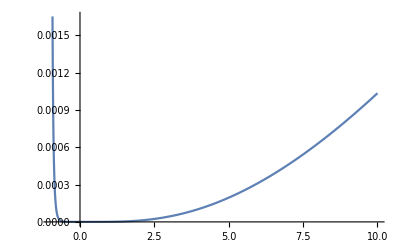

```mathematica
Plot[qiSpinUp[4,4,1,k], {k,-0.99,10}]
```

```mathematica
Table[qiSpinUp[i,i,1,k], {i,0,8}]
```

{(√((1/(2 1)-3/8 1)/(√(1+k) (1/1+1))) √(1-1^2/1^2) (1))/(((3+1)/(√1 11))^(1/4) √π),1/(1 √π),5,1/1,1/(1 √π)}
 |  |  |  |

```mathematica
Table[qiSpinDown[i,i,1,k], {i,0,8}]
```

{(√((1/(2 1)-3/8 1)/(√(1+k) (1/1+1))) √(1-1^2/1^2) (1))/(((3+1)/(√1 11))^(1/4) √π),1/(1 √π),5,1/1,1/(1 √π)}
 |  |  |  |